# Matura 2025

## Izpitna pola 1

## B)

### 1.

Naj bo
•  množica vseh praštevil, manjših od 20,
•  množica vseh deliteljev števila 12 in
•  množica vseh večkratnikov števila 3, manjših od 20.
Zapišite množice:
• ,
• ,
• ,
• .

```mathematica
a=Select[Range[20],PrimeQ]
```

{2,3,5,7,11,13,17,19}

```mathematica
b=Divisors[12]
```

{1,2,3,4,6,12}

```mathematica
c=Select[Range[20],m|->Divisible[m,3]]
```

{3,6,9,12,15,18}

```mathematica
Intersection[a,b]
```

{2,3}

```mathematica
Union[b,c]
```

{1,2,3,4,6,9,12,15,18}

### 2.

Izračunajte diskriminante in poiščite vse rešitve kvadratnih enačb.
• 
• 
•

```mathematica
TableForm[
Table[{izraz==0,Discriminant[izraz,x],Solve[izraz==0,x]},{izraz,{x^2-6x+9,x^2-3x-10,x^2-6x+10}}
],
TableDepth->2,
TableHeadings->{None,{"enačba","diskriminanta","ničli"}}
]
```

enačba | diskriminanta | ničli
9-6 x+x^2==0 | 0 | {{x→3},{x→3}}
-10-3 x+x^2==0 | 49 | {{x→-2},{x→5}}
10-6 x+x^2==0 | -4 | {{x→3-ⅈ},{x→3+ⅈ}}

### 3.

Na krožnici s središčem v izhodišču in polmerom 1 ležita točki  in . Točka  je pravokotna projekcija točke  na abscisno os, točka  je izhodišče. Kot .
Izračunajte koordinate točke  ter obseg in ploščino trikotnika .

```mathematica
a={-(√3)/2,1/2}
```

{-(√3)/2,1/2}

```mathematica
b={Cos[60Degree],Sin[60Degree]}
```

{1/2,(√3)/2}

```mathematica
c={0,0}
```

{0,0}

```mathematica
a0={a[[1]],0}
```

{-(√3)/2,0}

```mathematica
caa0=Triangle[{c,a,a0}]
```

Triangle[{{0,0},{-(√3)/2,1/2},{-(√3)/2,0}}]

```mathematica
Perimeter[caa0]
```

3/2+(√3)/2

```mathematica
Area[caa0]
```

(√3)/8

```mathematica
Graphics[{
Circle[{0,0},1],
Point[{a,b,c,a0}],
Line[{{c,a},{a,a0},{c,b}}],
Opacity[0.3],Blue,
caa0
},
Axes->True,AxesStyle
]
```

-Graphics-

### 5.

Dana je funkcija 

Izračunajte stacionarni točki in enačbo tangente v točki z absciso .

```mathematica
f[x_]:=x^2/(x-2)
```

```mathematica
stacionarni=Solve[f'[x]==0,x]
```

{{x→0},{x→4}}

```mathematica
dotikalisce={x->-2,y->f[-2]}
```

{x→-2,y→-1}

```mathematica
parametraTangente=Solve[{y==k x+m,k==f'[x]}/.dotikalisce,{k,m}]
```

{{k→3/4,m→1/2}}

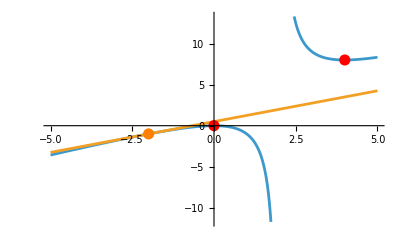

```mathematica
Plot[{
f[x],
(k x+m)/.parametraTangente
},{x,-5,5},Epilog->
{
PointSize[0.02],
Red,Point[{x,f[x]}/.stacionarni],
Orange,Point[{x,y}/.dotikalisce]
}
]
```

### 6.

Premica  je asimptota hiperbole s središčem v . Gorišči ležita na osi , točka  leži na hiperboli.
Zapišite enačbo hiperbole in njeno zrcaljenje preko simetrale lihih kvadrantov.

```mathematica
ClearAll[a,b]
```

```mathematica
parametriHiperbole=Solve[{(x^2/a^2-y^2/b^2==1)/.{x->√6,y->2 √3},b/a==2},{a,b}][[1]]
```

{a→-√3,b→-2 √3}

```mathematica
enacbaHiperbole=(x^2/a^2-y^2/b^2==1)/.parametriHiperbole
```

x^2/3-y^2/12==1

```mathematica
enacbaPrezrcaljeneHiperbole=enacbaHiperbole/.{x->y,y->x}
```

-x^2/12+y^2/3==1

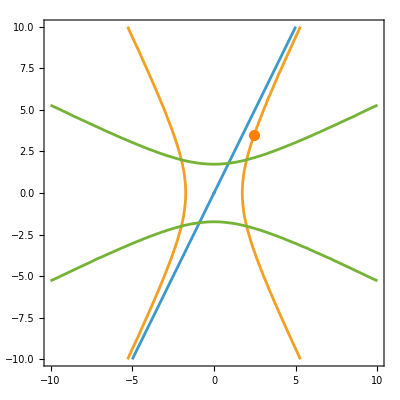

```mathematica
ContourPlot[{
y==2x,
enacbaHiperbole,
enacbaPrezrcaljeneHiperbole
},{x,-10,10},{y,-10,10},Axes->True,Epilog->{
Orange,PointSize[0.02],
Point[{√6,2 √3}]}
]
```

## C)

### 2.

Funkcija je podana s predpisom 

1. Izračunajte podane vrednosti funkcije, odvodov in integralov.
2. Naj bo  periodična funkcija s periodo 6, ki sovpada z  na .
   Izračunajte , preverite sodost in določite intervale padanja.

```mathematica
f[x_]:=Which[
0<=x<4,-√(-x^2+4x),
4<=x<5,3x-12,
5<=x<=6,-3x+18
]
```

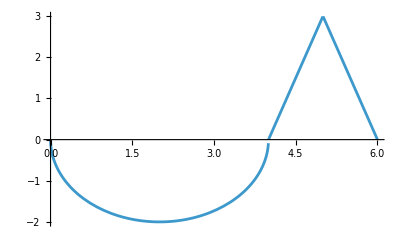

```mathematica
Plot[f[x],{x,0,6}]
```

```mathematica
TableForm[
Table[{izraz/.f0->HoldForm[f],izraz/.f0->f},{izraz,{
∫_0^6 f0[x]ⅆx,
f0[1/2],f0[11/2],
f0'[1],f0'[11/2],
f0''[9/2],
∫_0^2 f0[x]ⅆx,
∫_4^6 f0[x]ⅆx
}}],
TableHeadings->{None,{"izraz","vrednost"}}
]
```

izraz | vrednost
∫_0^6 f[x]ⅆx | 3-2 π
f[1/2] | -(√7)/2
f[11/2] | 3/2
f'[1] | -1/(√3)
f'[11/2] | -3
f''[9/2] | 0
∫_0^2 f[x]ⅆx | -π
∫_4^6 f[x]ⅆx | 3

```mathematica
g[x_]:=f[Mod[x,6]]
```

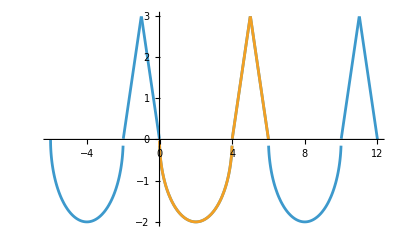

```mathematica
Plot[{g[x],f[x]},{x,-6,12}]
```

```mathematica
Integrate[g[x],{x,-2022,2022}]
```

∫_-2022^2022 Which[0≤Mod[x,6]<4,-√(-Mod[x,6]^2+4 Mod[x,6]),4≤Mod[x,6]<5,3 Mod[x,6]-12,5≤Mod[x,6]≤6,-3 Mod[x,6]+18]ⅆx

```mathematica
NIntegrate[g[x],{x,-2022,2022}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {86.82}. NIntegrate obtained -2896.8 and 287.118 for the integral and error estimates.

-2896.8

```mathematica
NIntegrate[g[x],{x,-2022,2022},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {710.8147614759430403317859260046133559061376482318944082269669119069226}. NIntegrate obtained -2314.792784264176229084378020577840124052293833103533926064062412337617 and 261.2363382343771843980431468462653030116130926546737708709787917988059 for the integral and error estimates.

-2314.7927842641762291

```mathematica
Mod[2022,6]
```

0

```mathematica
integralG=(4044/6)Integrate[f[x],{x,0,6}]
```

674 (3-2 π)

```mathematica
N[integralG]
```

-2212.87

## Izpitna pola 2

## B)

### 1.

Narišite premici z enačbama   
•   
• 
ter izračunajte ploščino trikotnika, ki ga premici oklepata z ordinatno osjo.

```mathematica
f1[x_]:=-3
f2[x_]:=-2x+3
```

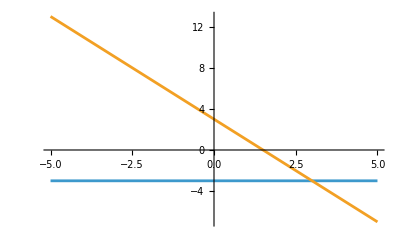

```mathematica
Plot[{f1[x],f2[x]},{x,-5,5}]
```

```mathematica
Solve[f1[x]==f2[x],x]
```

{{x→3}}

```mathematica
a={3,f1[3]}
```

{3,-3}

```mathematica
b={0,f1[0]}
```

{0,-3}

```mathematica
c={0,f2[0]}
```

{0,3}

```mathematica
Area[Triangle[{a,b,c}]]
```

9

### 3.

Dvakrat zapored vržemo pošteno igralno kocko. Izračunajte verjetnosti dogodkov: 
• A – obakrat je padla šestica,  
• B – vsaj enkrat je padla šestica,  
• C – po obeh metih je vsota pik največ 5.

```mathematica
Probability[kocka1==6&&kocka2==6,{kocka1\[Distributed]DiscreteUniformDistribution[{1,6}],kocka2\[Distributed]DiscreteUniformDistribution[{1,6}]}]
```

1/36

```mathematica
Probability[kocka1==6||kocka2==6,{kocka1\[Distributed]DiscreteUniformDistribution[{1,6}],kocka2\[Distributed]DiscreteUniformDistribution[{1,6}]}]
```

11/36

```mathematica
Probability[kocka1+kocka2<=5,{kocka1\[Distributed]DiscreteUniformDistribution[{1,6}],kocka2\[Distributed]DiscreteUniformDistribution[{1,6}]}]
```

5/18

### 4.

Stranice trikotnika  tvorijo aritmetično zaporedje z diferenco 3. Izračunajte in zapišite dolžine stranic trikotnika , če je njegov obseg enak 30. Na minuto natančno izračunajte še velikost največjega kota trikotnika .

```mathematica
ClearAll[a,b,c]
```

```mathematica
Solve[{b==a+3,c==b+3,a+b+c==30},{a,b,c}]
```

{{a→7,b→10,c→13}}

```mathematica
NSolve[(c^2==a^2+b^2-2 a b Cos[γ]&&0<γ<π)/.{a->7,b->10,c->13},γ,Reals]
```

{{γ→1.71414}}

```mathematica
N[Degree]
```

0.0174533

```mathematica
1.714143895700262/Degree
```

98.2132

### 5.

Vsaka od funkcij v preglednici ima natanko eno od naštetih lastnosti. Obkrožite jo. Primer v prvi vrstici je rešen. 
"Funkcijski predpis" | "Lastnost funkcije (izberite eno)"
 | "soda / liha / naraščajoča / padajoča"
 | "soda / liha / naraščajoča / padajoča"
 | "soda / liha / naraščajoča / padajoča"
 | "soda / liha / naraščajoča / padajoča"
 | "soda / liha / naraščajoča / padajoča"
 | "soda / liha / naraščajoča / padajoča"

```mathematica
ClearAll[f]
```

```mathematica
Table[
{
f[x]==g[x],
If[Reduce[g[x]==g[-x],x,Reals]==True,"soda","",""],
If[Reduce[g[x]==-g[-x],x,Reals]==True,"liha","",""],
If[Reduce[g'[x]>=0,x,Reals]==True,"naraščajoča","",""],
If[Reduce[g'[x]<=0,x,Reals]==True,"padajoča","",""]

},
{g,{
x|->x^2 Sin[x],
x|->2^-x,
x|->Cos[x],
x|->Log[2,x^2],
x|->Abs[x]-1,
x|->x+Cos[x]
}}
]//TableForm
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

f[x]==x^2 Sin[x] |  | liha |  | 
f[x]==2^-x |  |  |  | padajoča
f[x]==Cos[x] | soda |  |  | 
f[x]==Log[x^2]/Log[2] | soda |  |  | 
f[x]==-1+Abs[x] | soda |  |  | 
f[x]==x+Cos[x] |  |  | naraščajoča |

### 6.

V koordinatnem sistemu je narisana krivulja z enačbo  Označeni območji  in  v pravokotniku imata enako ploščino. Izračunajte .

```mathematica
ClearAll[f]
```

```mathematica
f[x_]:=x^3+a
```

```mathematica
resitev=Solve[∫_0^1 f[x]ⅆx==f[1]/2,a][[1,1]]
```

a→1/2

```mathematica
{obmocjeA,obmocjeB}={
ImplicitRegion[0<=x<=1&&0<=y<=f[x],{x,y}],
ImplicitRegion[0<=x<=1&&f[x]<=y<=f[1],{x,y}]
}/.resitev
```

{ImplicitRegion[0≤x≤1&&0≤y≤1/2+x^3,{x,y}],ImplicitRegion[0≤x≤1&&1/2+x^3≤y≤3/2,{x,y}]}

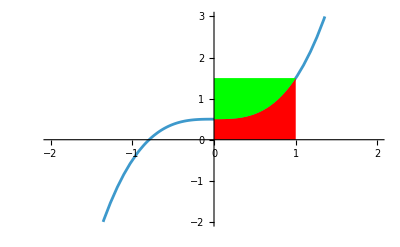

```mathematica
Show[{
Plot[f[x]/.resitev,{x,-2,2},PlotRange->{-2,3}],
Region[Style[obmocjeA,Red]],
Region[Style[obmocjeB,Green]]
}]
```

```mathematica
Area[obmocjeA]
```

3/4

```mathematica
Area[obmocjeB]
```

3/4

## C)

### 1.

Dani sta zaporedji s splošnima členoma   

1. Koliko členov zaporedja s splošnim členom  je večjih od ?
2. Izračunajte limito zaporedja s splošnim členom 
3. Dokažite, da je zaporedje s splošnim členom  padajoče. Določite natančno spodnjo in natančno zgornjo mejo tega zaporedja.

```mathematica
a[n_]:=√(4 n^2-n)
```

```mathematica
b[n_]:=2n
```

```mathematica
Reduce[1/a[n]>1/100,n,PositiveIntegers]
```

n==1||n==2||n==3||n==4||n==5||n==6||n==7||n==8||n==9||n==10||n==11||n==12||n==13||n==14||n==15||n==16||n==17||n==18||n==19||n==20||n==21||n==22||n==23||n==24||n==25||n==26||n==27||n==28||n==29||n==30||n==31||n==32||n==33||n==34||n==35||n==36||n==37||n==38||n==39||n==40||n==41||n==42||n==43||n==44||n==45||n==46||n==47||n==48||n==49||n==50

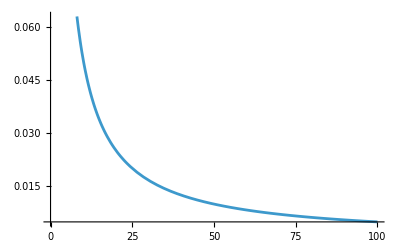

```mathematica
Plot[1/a[n],{n,0,100}]
```

```mathematica
Limit[a[n]-b[n],n->∞]
```

-1/4

```mathematica
g[n_]:=b[n]/a[n]^2
```

```mathematica
Reduce[g[n+1]<g[n],n,PositiveIntegers]
```

n∈ℤ&&n≥1

```mathematica
Minimize[g[n],n,PositiveIntegers]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{0,{n→∞}}

```mathematica
Maximize[g[n],n,PositiveIntegers]
```

{2/3,{n→1}}

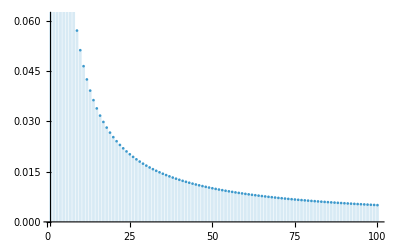

```mathematica
DiscretePlot[g[n],{n,1,100}]
```